To load the functionality for verifying operator identities via noncommutative Groebner bases computations, just load the OperatorGB package. This can be done by the following command, provided that the file OperatorGB.m and this file are located in the same directory:

```mathematica
SetDirectory[NotebookDirectory[]];
<<OperatorGB.m
```

Package OperatorGB version 1.2.0
Copyright 2020, Institute for Algebra, JKU
by Clemens Hofstadler, clemens.hofstadler@jku.at

We note that this documentation should be understandable without further theoretical knowledge; at least the first section, which shall be the standard use-case of this package. For the theory behind this package and further information/details we refer to  "this paper""this paper".

## Certifying operator identities

In this section, we describe the standard use-case of this package, which is to automatically prove operator identities.

We illustrate the functionality of the package and its usage on a concrete example. To this end, we assume that we are given two linear operators A:V → W and B:U→ V, together with inner inverses, denoted by A^- and B^-, respectively, i.e. operators satisfying A A^-A=A and B B^-B=B.

We want to prove that B^-A^- is an inner inverse of A B, i.e. that

							 A B B^-A^-A B = A B
							
holds, provided that the operator A^-A B B^- is idempotent. This means A^-A B B^- A^-A B B^- = A^-A B B^-.

To prove such an operator identity, first, all equations involved have to be translated into (noncommutative) polynomials. This can be done by uniformly replacing each operator by an indeterminate and forming the differences of the left and right hand side of each operator identity. Note that this also includes the identity operator. Then, also the properties of composition of the identity with other operators have to be added to the assumptions.

In our example, we replace A by a, B by b, A^- by a^- and  B^-by b^-.  Additionally, we also collect all our assumptions in a set named “assumptions”.  Also, note that we have to use Mathematica’s noncommutative multiplication to obtain noncommutative polynomials.

```mathematica
assumptions = {a**SuperMinus[a]**a-a,b**SuperMinus[b]**b-b,SuperMinus[a]**a**b**SuperMinus[b]**SuperMinus[a]**a**b**SuperMinus[b]-SuperMinus[a]**a**b**SuperMinus[b]};
claim = a**b**SuperMinus[b]**SuperMinus[a]**a**b-a**b;
```

We also have to construct a labelled quiver, which is a labelled directed multigraph. This quiver shall relate the indeterminates with the domains and codomains of the corresponding operators.

Such a quiver can be defined by providing a list of triples. For every operator L appearing in our operator identities, we have to provide a triple of the form {l,s,t}, where l is the name of the indeterminate that we have replaced L with, s is the codomain of L and t the domain of L. Hence, we can set up a quiver Q for our example as follows:

```mathematica
Q={{a,V,W},{SuperMinus[a],W,V},{b,U,V},{SuperMinus[b],V,U}};
```

Now, we can call the method “Certify”, which takes a set of assumptions, a claim (all in form of noncommutative polynomials) and a quiver Q as input and returns either a linear combination of the claim in terms of the assumptions, which proves that the  corresponding claimed operator identity is indeed a consequence of the assumed identities, or $Failed, which indicates that the program was not able to prove that the claimed identity follows from the assumptions.

```mathematica
Certify[assumptions,claim,Q]
```

{{a,-b+b**b^-**b,1},{-a**b**b^-**a^-**a,-b+b**b^-**b,1},{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-**b},{1,-a+a**a^-**a,b**b^-**b}}

In case of our example, we obtain a linear combination of the claim in terms of the assumptions in form of a list of triples. In other words, we get {{ a_1, f_1, b_1 },... ,{ a_n, f_n, b_n }} such that 
						claim = ∑_(i=1)^n a_i f_i b_i
and f_i∈ assumptions for 1 ≤ i ≤ n.

This linear combination serves as a certificate that the claimed operator identity is indeed a consequence of the assumed identities. We can also expand this linear combination and check that it indeed equals the claim.

```mathematica
MultiplyOut[%] === claim
```

True

## Certifying ideal membership

In this section, we discuss the algebraic computations done during the execution of the “Certify” command. To this end, we assume that the reader has a basic knowledge about Groebner bases in the free algebra.

From an algebraic point of view, verifying that a claimed operator identity is a consequence of certain assumptions, corresponds to showing the ideal membership of the (noncommutative) polynomial corresponding to this claim in the ideal generated by the polynomials corresponding to the assumptions. Although the ideal membership problem of noncommutative polynomials is undecidable in general, in practice it can often be solved with (partial) Groebner bases. Therefore, this package also provides functionality to compute (partial) Groebner bases in the free algebra.

To be able to compute (partial) Groebner bases of noncommutative polynomial ideals, the user first has to set up a corresponding noncommutative polynomial ring. This is done by providing a list of all indeterminates that the ring shall contain. In the following, we set up a noncommutative polynomial ring in the indeterminates  a, b, a^-, b^-.

```mathematica
SetUpRing[{a,SuperMinus[a],b,SuperMinus[b]}]
```

a < a^- < b < b^-

The monomial order in this polynomial ring is predefined to be degree lexicographic, where the indeterminates are ordered in ascending order corresponding to the input list of the “SetUpRing” method. Hence, in our case, we get  a < b < a^- < b^-.

The user has the option to change the monomial order. The second pre-defined order is a weighted degree lexicographic order. To switch to this order, the user has to execute the following command:

```mathematica
SortedQ = WeightedDegLex;
```

Then, additionally, a list of weights  {w_1, w_2,... } named “Weight” has to be provided, where w_1 corresponds to the weight of the first indeterminate in the input list of “SetUpRing”, w_2 to the second one and so on. For our example, we could set

```mathematica
Weight = {5,5,1,3};
```

Then a and b are weighted with a factor of 5,  a^- with a factor of 1 and b^- with a factor of 3.

Additionally, it is also possible to define a multigraded lexicographic order. This can be done by calling “SetUpRing” with two lists instead of one. For example,

```mathematica
SetUpRing[{a,SuperMinus[a]},{b,SuperMinus[b]}]
```

a < a^- << b < b^-

would given a block order consisting of two blocks; the first block of indeterminates being  a and   a^- and the second block  b and b^-, respectively.

To define an individual order, the user can also provide a binary function SortedQ[w,w'] acting on the set of all words that can be formed over the alphabet of indeterminates. It decides, when given two words w and w' as input, which of them is larger, by returning True if w ≤ w' and False otherwise. Note that for the function “SortedQ” a word w = x_i_1 x_i_2... x_i_nhas to be provided in form of a list {x_i_1, x_i_2,..., x_i_n}.

For now, however, we will stick to the degree lexicographic order.

```mathematica
SortedQ = DegLex;
```

An ideal in this polynomial ring can be defined simply by providing the generators as polynomials using Mathematica’s built in noncommutative multiplication. As an example, we consider the ideal generated by the polynomials that we also used in the previous section.

```mathematica
ideal = {a**SuperMinus[a]**a-a,b**SuperMinus[b]**b-b,SuperMinus[a]**a**b**SuperMinus[b]**SuperMinus[a]**a**b**SuperMinus[b]-SuperMinus[a]**a**b**SuperMinus[b]};
```

To now compute a Groebner basis of this ideal, we can call the method “Groebner”. Besides an ideal, this method takes an additional parameter (in this example named “cofactorsG”), which can basically be an arbitrary name and is not of importance for us now. For more information on this parameter please see the subsection “Additional information” at the end of this section.

```mathematica
G = Groebner[cofactorsG,ideal];
```

G now contains a Groebner basis of the ideal.

```mathematica
G
```

{-a+a**a^-**a,-b+b**b^-**b,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,-a**b**b^-+a**b**b^-**a^-**a**b**b^-,-a^-**a**b+a^-**a**b**b^-**a^-**a**b,-a**b+a**b**b^-**a^-**a**b}

We can use this Groebner basis to verify ideal membership. As an example, we want to show that the following polynomial f lies in our ideal.

```mathematica
f = a**b**SuperMinus[b]**SuperMinus[a]**a**b-a**b;
```

To this end, we have to compute a normal form of f with respect to G and check whether this normal form is zero. A normal form can be computed using the command “ReducedForm”. (The parameter “cofactorsF” handed to ReducedForm is not of interest for us now - for more information concerning this parameter we refer to the subsection “Additional information” at the end of this section)

```mathematica
ReducedForm[cofactorsF, G, f]
```

0

As we can see, we obtain zero, which shows that f indeed lies in our ideal.

### Additional information

In this subsection, we discuss the meaning of the parameters “cofactorsG” and “cofactorsF” that appeared above as well as some additional optional parameters that can be handed to the “Groebner” method.

First, we describe the “cofactorsG” argument given to the “Groebner” method. This argument just defines a name and can basically be chosen arbitrarily. In a list with this given name the cofactors of the new elements of the Groebner basis will be saved. So, executing

```mathematica
ideal = {a**SuperMinus[a]**a-a,b**SuperMinus[b]**b-b,SuperMinus[a]**a**b**SuperMinus[b]**SuperMinus[a]**a**b**SuperMinus[b]-SuperMinus[a]**a**b**SuperMinus[b]};
G = Groebner[cofactorsG,ideal];
```

does not only yield the Groebner basis G, but during this computation also a list named “cofactorsG” is generated. For each element g ∈ G, this list contains a list l of triples {a_i,f_i,b_i} forming a linear combination of g in terms of the generators f_i of the ideal and certain cofactors a_i,b_i.

```mathematica
cofactorsG
```

{{{1,-a+a**a^-**a,1}},{{1,-b+b**b^-**b,1}},{{1,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,1}},{{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,1},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-},{1,-a+a**a^-**a,b**b^-}},{{a^-**a,-b+b**b^-**b,1},{-a^-**a**b**b^-**a^-**a,-b+b**b^-**b,1},{1,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b}},{{a,-b+b**b^-**b,1},{-a**b**b^-**a^-**a,-b+b**b^-**b,1},{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-**b},{1,-a+a**a^-**a,b**b^-**b}}}

For example, the first list consists just of one triple and corresponds to the first element in G, which is also the first element of F,
the fourth list corresponds to the fourth element in G, i.e. the first element that has been added to the Groebner basis, and so on.

```mathematica
cofactorsG[[1]]
```

{{1,-a+a**a^-**a,1}}

```mathematica
cofactorsG[[4]]
```

{{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,1},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-},{1,-a+a**a^-**a,b**b^-}}

We can expand such a linear combination using the “MultiplyOut” command. In this case, we should obtain G[[4]] = a b b^-a^- a b b^-- a b b^-.

```mathematica
MultiplyOut[cofactorsG[[4]]]
```

-a**b**b^-+a**b**b^-**a^-**a**b**b^-

Note that if the parameter “cofactorsG” is already a list, then its content is cleared when it is handed to the “Groebner” method.

```mathematica
cofactorsG = {{1,2,3}};
G = Groebner[cofactorsG,ideal];
cofactorsG
```

{{{1,-a+a**a^-**a,1}},{{1,-b+b**b^-**b,1}},{{1,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,1}},{{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,1},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-},{1,-a+a**a^-**a,b**b^-}},{{a^-**a,-b+b**b^-**b,1},{-a^-**a**b**b^-**a^-**a,-b+b**b^-**b,1},{1,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b}},{{a,-b+b**b^-**b,1},{-a**b**b^-**a^-**a,-b+b**b^-**b,1},{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-**b},{1,-a+a**a^-**a,b**b^-**b}}}

Additionally, the Groebner method can also take several optional arguments. The full syntax of the Groebner command is

Groebner[cofactorsG, ideal, maxiter, MaxDeg->Infinity, Info->False, Parallel->True, Sorted->True, Criterion->True],

where the arguments “cofactorsG” and “ideal” are mandatory and have already been discussed. The additional parameter “maxiter” can be provided to determine how many iterations of the Buchberger algorithm are executed at most. By default this value is set to 10. It is also possible to set the OptionsPattern “MaxDeg” (default: Infinity), which determines the maximal degree of ambiguities that are considered during the Groebner basis computation (ambiguities with larger degree are simply ignored). Another OptionsPattern is “Info” (default: False), which, if set to True, prints information about the computation progress. Furthermore, the OptionsPattern “Parallel” (default: True) allows the user to specify whether all possible computations are executed in parallel or all computations are executed in series. The OptionPattern “Sorted” (default: True) sorts the ambiguities before processing if set to True. This might speed up the computation but when only a partial Groebner basis is computed, this might result in a different partial Groebner basis compared to when executing the same computation with “Sorted” disabled. The OptionsPattern “Criterion” (default: True) tries to detect and delete redundant ambiguities during the computation. In general, this speeds up the computation but again might result in a different partial Groebner basis.

Now, we come to the parameter “cofactorsF” of the “ReducedForm” method. When we compute a normal form f' of some polynomial f with respect to a set of polynomials G (typically G is a Groebner basis) using the “ReducedForm” command, we also have to provide an additional argument, previously named “cofactorsF”. Similar to “cofactorsG” in the “Groebner” command, this parameter also just defines a name and can therefore basically be chosen arbitrarily. In a list with the given name a linear combination of  f - f' in terms of G is saved.

```mathematica
f = a**b**SuperMinus[b]**SuperMinus[a]**a**b-a**b;
ReducedForm[cofactorsF,G,f]
```

0

Since the normal form  f' is zero in this case, we obtain a linear combination of f in terms of G. This linear combination is saved in a list named “cofactorsF” and is in this case just one triple as f is an element of G.

```mathematica
cofactorsF
```

{{1,-a**b+a**b**b^-**a^-**a**b,1}}

However, usually we want to have a linear combination only consisting of the generators of the ideal and not in terms of a Groebner basis. This can be achieved using the method Rewrite[cofactorsF,cofactorsG], where “cofactorsG” is the list that we obtained from calling Groebner[cofactorsG,ideal]. Since we now already have a list named “cofactorsG”, we first have to reset it  to the empty list.

```mathematica
cofactorsG = {};
G = Groebner[cofactorsG,ideal];
Rewrite[cofactorsF,cofactorsG]
```

{{a,-b+b**b^-**b,1},{-a**b**b^-**a^-**a,-b+b**b^-**b,1},{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-**b},{1,-a+a**a^-**a,b**b^-**b}}

The resulting list consists only of triples {a_i,f_i,b_i}, where a_i,b_i are certain cofactors and the f_i are the monic generators of the ideal that we started with. We can check that this linear combination still yields the polynomial f that we initially reduced:

```mathematica
MultiplyOut[%] === f
```

True

## Compatibility with Quivers

For details about the notions appearing in this section, we refer to  "this paper""this paper".

To infer statements about operators from a verified ideal membership of (noncommutative) polynomials, (uniform) compatibility of the polynomials involved with a quiver is required. Checking this compatibility can also be done using this package.

To this end, first of all a quiver has to be defined by providing a list of triples of the form {l,s,t}, where l is the label of an edge, s is the source and t the target of the corresponding edge. As an example, we set up the following quiver Q.

```mathematica
Q={{a,V,W},{SuperMinus[a],W,V},{b,U,V},{SuperMinus[b],V,U}};
```

To get a better overview, we can plot the quiver.

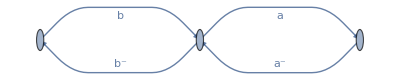

```mathematica
PlotQuiver[Q]
```

Given a quiver and a polynomial f, we can compute the set of signatures of f. The corresponding function to do this is called “QSignature” and can be called with a single polynomial...

```mathematica
f = a**b**SuperMinus[b]**SuperMinus[a]**a**b-a**b;
QSignature[f,Q]
```

{{U,W}}

...or with a list of polynomials

```mathematica
g =  b**SuperMinus[b]**b**SuperMinus[b]+ 1;
QSignature[{f,g},Q]
```

{{{U,W}},{{V,V}}}

The result of this function is the signature of each of the input polynomials given as a list of pairs. If the signature of a polynomial f is non-empty, f is compatible with the corresponding quiver. A stronger notion of compatibility is uniform compatibility. Both, compatibility as well as uniform compatibility of a polynomial with a quiver, can be tested explicitly using the functions  “CompatibleQ” and “UniformlyCompatibleQ”, respectively, which return True in the affirmative case and False otherwise.

```mathematica
CompatibleQ[f,Q]
UniformlyCompatibleQ[f,Q]
```

True

True

```mathematica
CompatibleQ[g,Q]
UniformlyCompatibleQ[g,Q]
```

True

False

### Quivers with non-unique labels

All functionality described in this section is also available for quiver with non-unique labels. Hence, we can also set up a quiver as follows:

```mathematica
Q2={{a,V,W},{SuperMinus[a],W,V},{b,U,V},{SuperMinus[b],V,U},{a,X,W}};
```

This yields a quiver where two different edges are labelled with a.

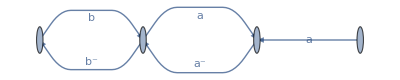

```mathematica
PlotQuiver[Q2]
```

As before, we can also compute the set of signatures of different polynomials with respect to Q2 ...

```mathematica
f = a**SuperMinus[a]**a - a;
g =  b**SuperMinus[b]**b**SuperMinus[b]+ 1;
QSignature[f,Q2]
QSignature[g,Q2]
```

{{V,W},{X,W}}

{{V,V}}

...  and check whether they are (uniformly) compatible with Q2.

```mathematica
CompatibleQ[{f,g},Q2]
UniformlyCompatibleQ[{f,g},Q2]
```

True

False

## Certify for the advanced user

In the first section, we have described the basic use of the “Certify” command, which provides a simple and fast way to  automatically prove operator identities. In this section, we present some additional parameters that can be set when calling “Certify” in order to obtain more information or speed up the computation.

In fact, the full syntax of the Certify command is

Certify[assumptions, claim, Q, MaxIter->10, MaxDeg->Infinity, MultiLex->False, Info->False, Parallel->True, Sorted->True, Criterion->True],

where the arguments “assumptions”, “claim” and “Q” are mandatory and have already been discussed. We note that “claim” does not necessarily have to be only a single polynomial. In fact, “claim” can also be a list of polynomials. We illustrate this on the example presented in the first section, where we add a second claim f_2.

```mathematica
assumptions = {a**SuperMinus[a]**a-a,b**SuperMinus[b]**b-b,SuperMinus[a]**a**b**SuperMinus[b]**SuperMinus[a]**a**b**SuperMinus[b]-SuperMinus[a]**a**b**SuperMinus[b]};
Q={{a,V,W},{SuperMinus[a],W,V},{b,U,V},{SuperMinus[b],V,U}};
Subscript[f, 1]= a**b**SuperMinus[b]**SuperMinus[a]**a**b-a**b;
Subscript[f, 2] = -SuperMinus[a]**a**b+SuperMinus[a]**a**b**SuperMinus[b]**SuperMinus[a]**a**b;
result = Certify[assumptions,{Subscript[f, 1],Subscript[f, 2]},Q]
```

{{{a,-b+b**b^-**b,1},{-a**b**b^-**a^-**a,-b+b**b^-**b,1},{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-**b},{1,-a+a**a^-**a,b**b^-**b}},{{a^-**a,-b+b**b^-**b,1},{-a^-**a**b**b^-**a^-**a,-b+b**b^-**b,1},{1,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b}}}

Now, the output is a list of lists of triples, where the i-th entry forms a linear combination of the i-th entry of “claim”.

```mathematica
MultiplyOut[result[[1]]] === Subscript[f, 1]
MultiplyOut[result[[2]]] === Subscript[f, 2]
```

True

True

Internally, “Certify” first checks whether all assumptions are uniformly compatible and all claims are compatible with the input quiver Q, then it computes a (partial) Groebner basis of the ideal generated by the assumptions and tries to verify the ideal membership of the claims in this ideal. Finally, it rewrites the linear combinations that it obtained during this Groebner basis and reduction computations and returns them.

If one of these steps fail, in particular, if only one step fails for a single polynomial contained in “claim”, the program returns $Failed.

```mathematica
Certify[assumptions,{Subscript[f, 1]+a**b,Subscript[f, 2]},Q]
```

$Failed

To receive more information about the output the optional parameter “Info” (default: False) can be set to True. This then also prints information about the computational progress. If “Info” is set to False no information about the internal computations is given and the output is either a linear combination of the claim(s)in terms of the assumptions or $Failed (as discussed in the first section). If “Info” is set to True, detailed information about the computational progress is given and the output is of the form {S_A,S_C,red, linearComb}, where S_A is a list containing the signatures of each element in “assumptions” with respect to Q,  S_C is a list containing the signatures of each element in “claim” with respect to Q, “red” is a list {f_1', ... , f_n'} containing a normal form f_i' of each element f_i in “claim” with respect to a (partial) Groebner basis and “linearComb” is a list of linear combinations such that the i-th entry of “linearComb” forms a linear combination of f_i- f_i'.

```mathematica
result = Certify[assumptions,{Subscript[f, 1],Subscript[f, 2]},Q,Info->True]
```

Using the following monomial ordering:

a < a^- < b < b^-

Interreduced the input from 3 polynomials to 3.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 3 elements in the beginning.

5 ambiguities in total (computation took 0.003352)

Removed 0 ambiguities in 0.000312

Generating S-polys: 0.005732 (2 in total)

Reducing S-polys: 0.000246 (2 remaining)

The second reduction took 0.054318

Iteration 1 finished. G has now 5 elements

Starting iteration 2...

G has 5 elements in the beginning.

15 ambiguities in total (computation took 0.012188)

Removed 4 ambiguities in 0.000923

Generating S-polys: 0.009397 (4 in total)

Reducing S-polys: 0.000427 (2 remaining)

The second reduction took 0.073194

Iteration 2 finished. G has now 6 elements

Done! All claims were successfully reduced to 0.

{{{{V,W}},{{U,V}},{{V,V}}},{{{U,W}},{{U,V}}},{0,0},{{{a,-b+b**b^-**b,1},{-a**b**b^-**a^-**a,-b+b**b^-**b,1},{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-**b},{1,-a+a**a^-**a,b**b^-**b}},{{a^-**a,-b+b**b^-**b,1},{-a^-**a**b**b^-**a^-**a,-b+b**b^-**b,1},{1,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b}}}}

It follows from

```mathematica
result[[3]]
```

{0,0}

that both claims could be reduced to zero by a (partial) Groebner basis. Additionally, result[[4]] contains as its first element a linear combination of f_1in terms of the elements in “assumptions” and as its second element a linear combination of f_2in terms of the elements in “assumptions”.

```mathematica
MultiplyOut[result[[4,1]]] === Subscript[f, 1]
MultiplyOut[result[[4,2]]] === Subscript[f, 2]
```

True

True

Note that if “Info” is set to True and a claim cannot be reduced to zero, we do not obtain $Failed but the (non-zero) normal form.

```mathematica
Certify[assumptions,Subscript[f, 1]+ a**b,Q,Info->True]
```

Using the following monomial ordering:

a < a^- < b < b^-

Interreduced the input from 3 polynomials to 3.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 3 elements in the beginning.

5 ambiguities in total (computation took 0.003141)

Removed 0 ambiguities in 0.000284

Generating S-polys: 0.005467 (2 in total)

Reducing S-polys: 0.000228 (2 remaining)

The second reduction took 0.07887

Iteration 1 finished. G has now 5 elements

Starting iteration 2...

G has 5 elements in the beginning.

15 ambiguities in total (computation took 0.012703)

Removed 4 ambiguities in 0.000606

Generating S-polys: 0.008676 (4 in total)

Reducing S-polys: 0.000412 (2 remaining)

The second reduction took 0.072746

Iteration 2 finished. G has now 6 elements

Starting iteration 3...

G has 6 elements in the beginning.

12 ambiguities in total (computation took 0.013646)

Removed 4 ambiguities in 0.000922

Generating S-polys: 0.008774 (2 in total)

Reducing S-polys: 0.000265 (0 remaining)

Starting iteration 4...

G has 6 elements in the beginning.

5 ambiguities in total (computation took 0.004496)

Removed 0 ambiguities in 0.00047

Generating S-polys: 0.005759 (0 in total)

Reducing S-polys: 0.000026 (0 remaining)

Starting iteration 5...

G has 6 elements in the beginning.

5 ambiguities in total (computation took 0.005466)

Removed 0 ambiguities in 0.000464

Generating S-polys: 0.006457 (0 in total)

Reducing S-polys: 0.000025 (0 remaining)

Starting iteration 6...

G has 6 elements in the beginning.

5 ambiguities in total (computation took 0.004343)

Removed 0 ambiguities in 0.000417

Generating S-polys: 0.005472 (0 in total)

Reducing S-polys: 0.000025 (0 remaining)

Starting iteration 7...

G has 6 elements in the beginning.

5 ambiguities in total (computation took 0.009837)

Removed 0 ambiguities in 0.000734

Generating S-polys: 0.007492 (0 in total)

Reducing S-polys: 0.000029 (0 remaining)

Starting iteration 8...

G has 6 elements in the beginning.

5 ambiguities in total (computation took 0.00488)

Removed 0 ambiguities in 0.000444

Generating S-polys: 0.005569 (0 in total)

Reducing S-polys: 0.000021 (0 remaining)

Starting iteration 9...

G has 6 elements in the beginning.

5 ambiguities in total (computation took 0.004277)

Removed 0 ambiguities in 0.000456

Generating S-polys: 0.008576 (0 in total)

Reducing S-polys: 0.000131 (0 remaining)

Starting iteration 10...

G has 6 elements in the beginning.

5 ambiguities in total (computation took 0.005033)

Removed 0 ambiguities in 0.000504

Generating S-polys: 0.005813 (0 in total)

Reducing S-polys: 0.000023 (0 remaining)

Done! Not all claims could be reduced to 0.

{{{{V,W}},{{U,V}},{{V,V}}},{{U,W}},a**b,{{a,-b+b**b^-**b,1},{-a**b**b^-**a^-**a,-b+b**b^-**b,1},{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-**b},{1,-a+a**a^-**a,b**b^-**b}}}

The optional arguments “MaxIter” (default: 10), “MaxDeg” (default: Infinity), “Parallel” (default: True), “Sorted” (default: True) and “Criterion” (default: True) are the same as for the “Groebner” method (see subsection “Additional information” at the end of “Certifying ideal membership”).

The final optional parameter “MultiLex” (default: False) determines whether a degree lexicographic (default) or a multigraded lexicographic order is used to compute the (partial) Groebner basis. If “MultiLex” is set to True, a multigraded order is used, where the first block of variables contains all indeterminates that appear in “claim” and the second block consists of the remaining variables. Setting “MultiLex” to True might speed up the computation.

## Useful auxiliary functions

The package also provides some auxiliary functions which shall make the life of the user a bit easier when it comes to entering the polynomials for the Groebner/Certify command. In particular, we provide functionality to easily work with adjoint operators, a function to automatically generate the 4 defining identities of the Moore-Penrose inverse and a function to generate the trivial quiver for a given set of polynomials.

#### Adjoint operator

In many operator identities the adjoint operator A^* of an operator A appears. Our package provides some functionality to work with these adjoint operators, such as automatically expanding the adjoint of products or sums. To this end, an adjoint operator A^* has to be translated to adj[a]. Also products like (A B)^* can directly be translated to adj[a**b] and the package then expands this product automatically. Similarly, sums can be entered as adj[a+b], which then gets automatically processed to adj[a] + adj[b].

```mathematica
adj[a**b]
```

adj[b]**adj[a]

```mathematica
adj[2**a + a**b**c]
```

adj[a]**2+adj[c]**adj[b]**adj[a]

Furthermore, when an equation holds, then also the adjoint equation holds. So, when we have assumptions involving adjoint operators we often have to add the adjoint statements to our assumptions.  This process can be quite tedious when this has to be done by hand. So, we provide a function named AddAdj[F] that takes a set of polynomials F and returns a set containing F and all adjoint statements of F.

```mathematica
PinvA = {-a+a**SuperDagger[a]**a,SuperDagger[a]**a**SuperDagger[a]-SuperDagger[a],-a**SuperDagger[a]+adj[SuperDagger[a]]**adj[a],adj[a]**adj[SuperDagger[a]]-SuperDagger[a]**a};
```

```mathematica
assumptions = AddAdj[PinvA]
```

{-a+a**a^†**a,a^†**a**a^†-a^†,-a**a^†+adj[a^†]**adj[a],adj[a]**adj[a^†]-a^†**a,-adj[a]+adj[a]**adj[a^†]**adj[a],-adj[a^†]+adj[a^†]**adj[a]**adj[a^†],a**a^†-adj[a^†]**adj[a],-adj[a]**adj[a^†]+a^†**a}

#### Moore-Penrose identities

Often, we have to translate operator identities that involve the Moore-Penrose inverse A^† of an operator A. To quickly generate all 4 defining equations of A^† we provide the function Pinv[a] that takes a variable a and returns the 4 defining equations for the Moore-Penrose inverse of a. In this case, a new variable for the Moore-Penrose inverse will be introduced, namely a^†.

```mathematica
Pinv[a]
```

{-a+a**a^†**a,a^†**a**a^†-a^†,-a**a^†+adj[a^†]**adj[a],adj[a]**adj[a^†]-a^†**a}

```mathematica
Pinv[b]
```

{-b+b**b^†**b,b^†**b**b^†-b^†,-b**b^†+adj[b^†]**adj[b],adj[b]**adj[b^†]-b^†**b}

In some identities also the Moore-Penrose inverse of a product A B  appears. When we translate such an operator equation, we of course have to provide the 4 defining equations for (A B)^† but we also have to introduce a new variable for  the whole product (A B)^†. And in this case, we explicitly have to provide the name for this new variable by passing a second argument to Pinv. For example, by calling Pinv[a**b, a a b b], we obtain the 4 defining Moore-Penrose equations for (a b)^† and a new variable named a a b b will be introduced to denote (a b)^†.

```mathematica
Pinv[a**b,aabb]
```

{-a**b+a**b**aabb**a**b,-aabb+aabb**a**b**aabb,-a**b**aabb+adj[aabb]**adj[b]**adj[a],-aabb**a**b+adj[b]**adj[a]**adj[aabb]}

Only calling Pinv[a**b] can cause problems in further computations!

#### Trivial quiver

Often, we want to use the Certify command to quickly check whether a given set of assumptions implies some claims, without worrying about setting up a “correct” quiver that really captures all information about the domains and codomains of the operators involved. In this case, we can quickly set up a trivial quiver with which all polynomials are (uniformly) compatible. To this end, we provide the function TrivialQuiver[F], that takes a list of polynomials F and outputs a trivial quiver whose labels contain all variables appearing in the polynomials in F. Typically, this set F consists of all our assumptions and all claims.

```mathematica
assumptions = {a**b+c**adj[d],a**ab**c**d};
claims = {c**d**a**ab-b**c**SuperDagger[a]};
```

```mathematica
Q = TrivialQuiver[Join[assumptions,claims]]
```

{{a,1,1},{b,1,1},{c,1,1},{adj[d],1,1},{ab,1,1},{d,1,1},{a^†,1,1}}